## Governing ODE and BCs

```mathematica
eqn = D[y[x] D[y[x],x],x]*k + α* y[x]*Sin[θ] - α*Cos[θ]*y[x]*y'[x] == 1
BCs = {y[0]==1,y[1]==0.01};
```

α Sin[θ] y[x]-α Cos[θ] y[x] y'[x]+k (y'[x]^2+y[x] y''[x])==1

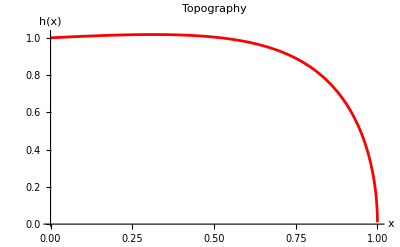

```mathematica
(*Solve numerically*)
Aval = 5;(*ρg/τ - ratio of gravity to yield stress*)
thetaval = π/10;(*slope of the flow*)
kval = 1.0;(*0.5<k<1 - corresponds to the viscous term in the z-momentum equation*)
numSol=NDSolve[{eqn/.{α->Aval,θ->thetaval,k->kval},BCs},y[x],{x,0,1},MaxSteps->∞];
Plot[Evaluate[y[x]/. numSol],{x,0,1},AxesLabel->{"x","h(x)"},PlotStyle->Red,PlotLabel->"Topography",PlotRange->Full]
```

## Simplifying conditions

### - Small slopes (θ = 0)

-α y[x] y'[x]+k (y'[x]^2+y[x] y''[x])==1

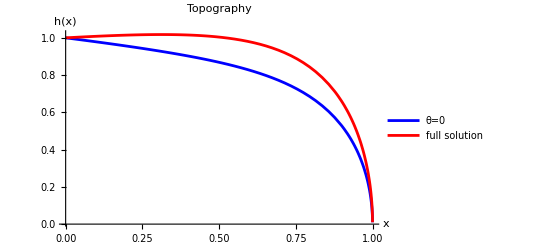

```mathematica
eqn = D[y[x] D[y[x],x],x]*k - α*y[x]*y'[x] == 1
(*Solve numerically*)
numSolt0=NDSolve[{eqn/.{α->Aval,k->kval},BCs},y[x],{x,0,1}];
Plot[{Evaluate[y[x]/. numSolt0],Evaluate[y[x]/. numSol]},{x,0,1},AxesLabel->{"x","h(x)"},PlotStyle->{Blue,Red},PlotLabel->"Topography",PlotRange->Full,PlotLegends->{"θ=0","full solution"}]
```

### - vanishing gravitational stress (θ ~ 0, α ~ 0)

-α y[x] y'[x]+k (y'[x]^2+y[x] y''[x])==1

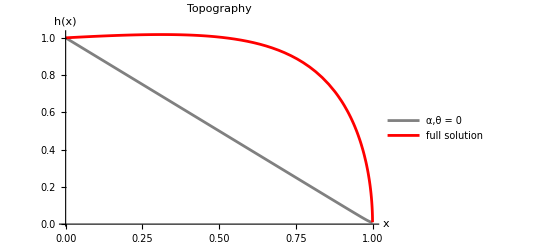

```mathematica
eqn = D[y[x] D[y[x],x],x]*k -α*y[x]*y'[x]== 1
(*Solve numerically*)
(*Analytically this solution is simply h(x) = (1-x)/[k]^0.5 with h(0) = 1/k^0.5*)
numSola0=NDSolve[{eqn/.{k->kval,α->0.0001},BCs},y[x],{x,0,1}];
Plot[{Evaluate[y[x]/. numSola0],Evaluate[y[x]/. numSol]},{x,0,1},AxesLabel->{"x","h(x)"},PlotStyle->{Gray,Red},PlotLabel->"Topography",PlotRange->Full,PlotLegends->{"α,θ = 0","full solution"}]
```

```mathematica
eqn = D[y[x] D[y[x],x],x]*k -α*y[x]*y'[x]== 1
sola0 = DSolve[{eqn,y[1]==0},y,{x,0,1}]
(*Note here that y[0] = 1/[α*Sqrt[2(α+k*exp(α/k))]]*)
```

-α y[x] y'[x]+k (y'[x]^2+y[x] y''[x])==1

Power::infy: Infinite expression 1/0 encountered.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{y→Function[{x},-(ⅈ √(-2 ⅇ^((α (1+C[2]))/k) k+2 ⅇ^((α (x+C[2]))/k) k+2 α (-1+x+C[2])-2 k Log[ⅇ^((α C[2])/k)]))/α]},{y→Function[{x},(ⅈ √(-2 ⅇ^((α (1+C[2]))/k) k+2 ⅇ^((α (x+C[2]))/k) k+2 α (-1+x+C[2])-2 k Log[ⅇ^((α C[2])/k)]))/α]}}